```mathematica
gpd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-t-up-xi1-baryon.wdx"];
Hdg1=Query[1,1]@gpd;
Hdg2=Query[1,2]@gpd;
Her=Query[1,3]@gpd;
Hda=Query[1,4]@gpd;
Edg1=Query[2,1]@gpd;
Edg2=Query[2,2]@gpd;
Eer=Query[2,3]@gpd;
Eda=Query[2,4]@gpd;
Hdgf1=Interpolation[Flatten[Hdg1,1]];
Hdgf2=Interpolation[Flatten[Hdg2,1]];
Herf=Interpolation[Flatten[Her,1]];
Hdaf=Interpolation[Flatten[Hda,1]];
Edgf1=Interpolation[Flatten[Edg1,1]];
Edgf2=Interpolation[Flatten[Edg2,1]];
Eerf=Interpolation[Flatten[Eer,1]];
Edaf=Interpolation[Flatten[Eda,1]];
```

```mathematica
gpdd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-u-up-xi1-baryon.wdx"];
Hdg1=Query[1,1]@gpdd;
Hdg2=Query[1,2]@gpdd;
Her=Query[1,3]@gpdd;
Hda=Query[1,4]@gpdd;
Edg1=Query[2,1]@gpdd;
Edg2=Query[2,2]@gpdd;
Eer=Query[2,3]@gpdd;
Eda=Query[2,4]@gpdd;
Hdgf1=Interpolation[Flatten[Hdg1,1]];
Hdgf2=Interpolation[Flatten[Hdg2,1]];
Herf=Interpolation[Flatten[Her,1]];
Hdaf=Interpolation[Flatten[Hda,1]];
Edgf1=Interpolation[Flatten[Edg1,1]];
Edgf2=Interpolation[Flatten[Edg2,1]];
Eerf=Interpolation[Flatten[Eer,1]];
Edaf=Interpolation[Flatten[Eda,1]];
```

```mathematica
Herall[x_,t_]:=Herf[x,t]+Hdaf[x,t];
Eerall[x_,t_]:=Eerf[x,t]+Edaf[x,t];
```

```mathematica
(*Edgf=Interpolation[Flatten[Edg,1]];
Eerf=Interpolation[Flatten[Eer,1]];
Edaf=Interpolation[Flatten[Eda,1]];*)
```

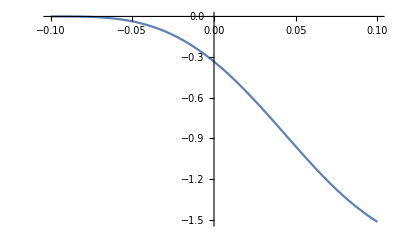

```mathematica
Plot[-I*Herf[x,-1],{x,-0.1,0.1}]
```

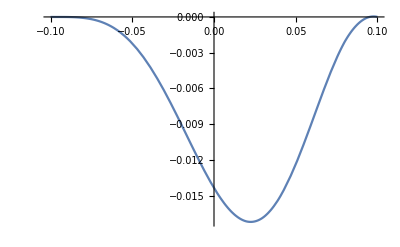

```mathematica
Plot[-I*Hdaf[x,-1],{x,-0.1,0.1}]
```

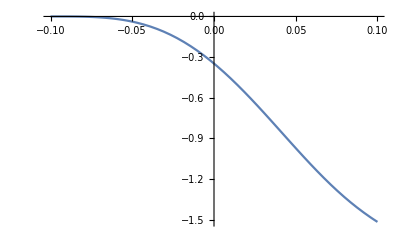

```mathematica
Plot[-I*Herall[x,-1],{x,-0.1,0.1}]
```

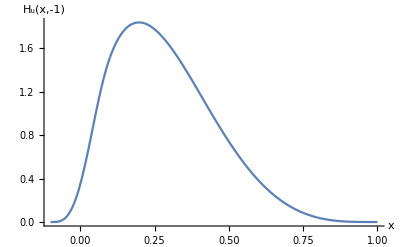

```mathematica
pHu2d=Show[Plot[I*Hdgf2[x,-1],{x,0.1,0.8},PlotRange->All],Plot[I*Hdgf1[x,-1],{x,0.8,1},PlotRange->All],Plot[I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","H_u(x,-1)"}]
```

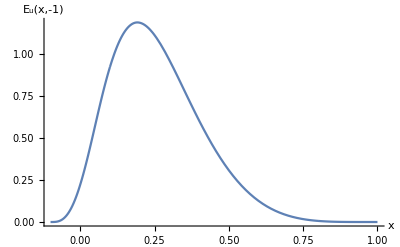

```mathematica
pEu2d=Show[Plot[I*Edgf2[x,-1],{x,0.1,0.8},PlotRange->All],Plot[I*Edgf1[x,-1],{x,0.8,1},PlotRange->All],Plot[I*Eerall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","E_u(x,-1)"}]
```

```mathematica
pHu3d=Show[Plot3D[I*Hdgf2[x,t],{x,0.1,0.8},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[I*Hdgf1[x,t],{x,0.8,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[I*Herall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","H_u(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
pEu3d=Show[Plot3D[I*Edgf2[x,t],{x,0.1,0.8},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[I*Edgf1[x,t],{x,0.8,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[I*Eerall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","E_u(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0598214,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[-I*Herf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

-Graphics3D-

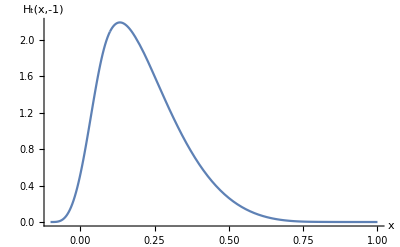

```mathematica
pHt2d=Show[Plot[-I*Hdgf2[x,-1],{x,0.1,0.8},PlotRange->All],Plot[-I*Hdgf1[x,-1],{x,0.8,1},PlotRange->All],Plot[-I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","H_t(x,-1)"}]
```

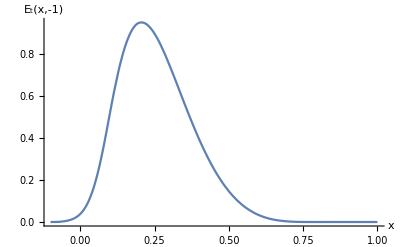

```mathematica
pEt2d=Show[Plot[-I*Edgf2[x,-1],{x,0.1,0.8},PlotRange->All],Plot[-I*Edgf1[x,-1],{x,0.8,1},PlotRange->All],Plot[-I*Eerall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","E_t(x,-1)"}]
```

```mathematica
pHt3d=Show[Plot3D[-I*Hdgf2[x,t],{x,0.1,0.8},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Hdgf1[x,t],{x,0.8,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Herall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","H_t(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
pEt3d=Show[Plot3D[-I*Edgf2[x,t],{x,0.1,0.8},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Edgf1[x,t],{x,0.8,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Eerall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","E_t(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
tpathH3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"t-Hu-0.1-baryon.pdf"}];
tpathE3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"t-Eu-0.1-baryon.pdf"}];
```

```mathematica
tpathH=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"t-Hu-0.1-2d-baryon.pdf"}];
tpathE=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"t-Eu-0.1-2d-baryon.pdf"}];
```

```mathematica
upathH3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"u-Hu-0.1-baryon.pdf"}];
upathH=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"u-Hu-0.1-2d-baryon.pdf"}];
upathE3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"u-Eu-0.1-baryon.pdf"}];
upathE=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"u-Eu-0.1-2d-baryon.pdf"}];
```

```mathematica
Export[upathH3d,pHu3d]
Export[upathH,pHu2d]
Export[upathE3d,pEu3d]
Export[upathE,pEu2d]
```

G:\calc-online\gpd\3dre\228test\u-Hu-0.1-baryon.pdf

G:\calc-online\gpd\3dre\228test\u-Hu-0.1-2d-baryon.pdf

G:\calc-online\gpd\3dre\228test\u-Eu-0.1-baryon.pdf

G:\calc-online\gpd\3dre\228test\u-Eu-0.1-2d-baryon.pdf

```mathematica
Export[tpathH3d,pHt3d]
Export[tpathH,pHt2d]
Export[tpathE3d,pEt3d]
Export[tpathE,pEt2d]
```

G:\calc-online\gpd\3dre\228test\t-Hu-0.1-baryon.pdf

G:\calc-online\gpd\3dre\228test\t-Hu-0.1-2d-baryon.pdf

G:\calc-online\gpd\3dre\228test\t-Eu-0.1-baryon.pdf

G:\calc-online\gpd\3dre\228test\t-Eu-0.1-2d-baryon.pdf

```mathematica
SubscriptBox["H",e]//DisplayForm
```

H_e

```mathematica
Plot3D[Eerf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0598214,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[-I*Eerf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0598214,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

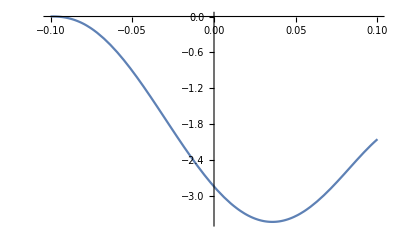

```mathematica
Plot[-I*Chop[Eerf[x,-0.1],10^-9],{x,-0.1,0.1}]
```

```mathematica
Eerf[0,-0.1]
```

0.-2.83547 ⅈ

```mathematica
Eerf[0.02,-0.1]
```

-8.32662×10^-26-3.30567 ⅈ

```mathematica
Eerf[-0.005,-0.1]
```

-1.49999×10^-11-2.67216 ⅈ

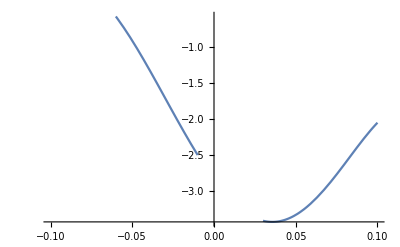

```mathematica
Plot[-I*Eerf[x,-0.1],{x,-0.1,0.1}]
```

```mathematica
Plot3D[I*Herf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

-Graphics3D-